# Slepton-side γ-radiation

## Load FeynCalc

```mathematica
description="Photon radiation correction to slepton pair production.";
If[$FrontEnd===Null,
$FeynCalcStartupMessages=False;
Print[description];
];
If[$Notebooks===False,
$FeynCalcStartupMessages=False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## Calculate the squared amplitude

### Draw diagrams

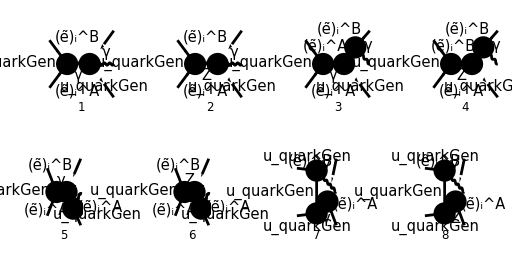

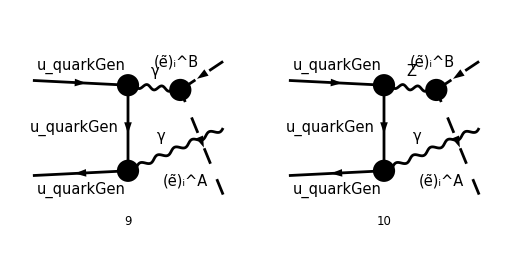

```mathematica
diags=InsertFields[
CreateTopologies[0,2->3],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4]}
];
Paint[
diags,
ColumnsXRows->{4,2},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[k1, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(1\)]\)"; 
MakeBoxes[k2, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(2\)]\)";
```

```mathematica
M[0]=FCFAConvert[
CreateFeynAmp[diags],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k,k2},
ChangeDimension->D,
UndoChiralSplittings->True,
(*List->False,*) (*NB! Messes with ordering of diagrams!*)
Contract->True,
DropSumOver->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

{-(4 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) e^3 δ_Col1Col2)/(3 (k+k_1+k_2)^2),(ⅈ (φ(-p_2)).((2 ⅈ (γ·ε^*(k)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·ε^*(k)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(2 (φ(-p_2)).(γ·(k+k_1-k_2)).(φ(p_1)) IndexDelta(A,B) (-(k·ε^*(k))-2 (k_1·ε^*(k))) e^3 δ_Col1Col2)/(3 (k+k_1+k_2)^2 ((-k-k_1)^2-(MSf(A,2,i))^2)),(ⅈ (φ(-p_2)).((2 ⅈ (γ·(k+k_1-k_2)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(k+k_1-k_2)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-(k·ε^*(k))-2 (k_1·ε^*(k))) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((-k-k_1)^2-(MSf(B,2,i))^2) ((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(2 (φ(-p_2)).(γ·(k-k_1+k_2)).(φ(p_1)) IndexDelta(A,B) (-(k·ε^*(k))-2 (k_2·ε^*(k))) e^3 δ_Col1Col2)/(3 (k+k_1+k_2)^2 ((k+k_2)^2-(MSf(A,2,i))^2)),(ⅈ (φ(-p_2)).((2 ⅈ (γ·(k-k_1+k_2)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(k-k_1+k_2)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-(k·ε^*(k))-2 (k_2·ε^*(k))) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((k+k_2)^2-(MSf(A,2,i))^2) ((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(4 (φ(-p_2)).(γ·(k_2-k_1)).(γ·(k_1+k_2-p_2)).(γ·ε^*(k)).(φ(p_1)) IndexDelta(A,B) e^3 δ_Col1Col2)/(9 (k_1+k_2)^2 (-k_1-k_2+p_2)^2),(ⅈ (φ(-p_2)).((2 ⅈ (γ·(k_2-k_1)).(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ (γ·(k_2-k_1)).(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(γ·(k_1+k_2-p_2)).(γ·ε^*(k)).(φ(p_1)) e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(3 (-k_1-k_2+p_2)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(4 (φ(-p_2)).(γ·ε^*(k)).(γ·(k-p_2)).(γ·(k_2-k_1)).(φ(p_1)) IndexDelta(A,B) e^3 δ_Col1Col2)/(9 (k_1+k_2)^2 (p_2-k)^2),(ⅈ (φ(-p_2)).(γ·ε^*(k)).(γ·(k-p_2)).((2 ⅈ (γ·(k_2-k_1)).(γ̄)^6 e (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ (γ·(k_2-k_1)).(γ̄)^7 e (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) e^2 δ_Col1Col2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(3 (p_2-k)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))}

### Extract the fifth diagram, and change 2/3 to e_Q

```mathematica
Pair[Momentum[k],Momentum[Polarization[k,-I]]]=0; (*Lorenz gauge*)
M5[0]=Part[M[0],5];
M5[1]=M5[0] 3/2 SMP["e_Q"]
```

```mathematica
M5[1]//DiracSimplify
```

```mathematica
M5CC[1]=ComplexConjugate[M5[1]]
```

```mathematica
FCClearScalarProducts[];
SP[p1]=0;SP[p2]=0;SP[k]=0;
(*SetMandelstam*) (*How do I do this for a 2->3 process?*)
```

```mathematica
M5Squared[0]=(M5[1] M5CC[1])//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/(4 SUNN^2)]&//DoPolarizationSums[#,k,0]&(*//DiracSimplify//SUNSimplify[#,SUNNToCACF->False]&//Simplify*)
```

```mathematica
SP[p3]=MSf[B,2,i]^2; SP[p4]=MSf[A,2,i]^2; MSf[B,2,i]=MSf[A,2,i];
```

```mathematica
M5Squared[1]=M5Squared[0]//Simplify
```

```mathematica
Mandelstam23Rules={
Pair[Momentum[p1],Momentum[p2]]->s12/2,
Pair[Momentum[p1],Momentum[p3]]->(MSf[A,2,i]^2-t13)/2,
Pair[Momentum[p1],Momentum[p4]]->(MSf[A,2,i]^2-t14)/2,
Pair[Momentum[p2],Momentum[p3]]->(MSf[A,2,i]^2-t23)/2,
Pair[Momentum[p2],Momentum[p4]]->(MSf[A,2,i]^2-t24)/2
};
```

```mathematica
M5Squared[2]=M5Squared[1]//.Mandelstam23Rules//Simplify
```

### Extract all diagrams radiating from slepton A

Change  to for quark charge in photon diagram.

```mathematica
M5[0]=M[0][[5]] 3/2 SMP["e_Q"]
M6[0]=M[0][[6]]
```

-(e^3 e_Q δ_Col1Col2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_2·ε^*(k))) (φ(-p_2)).(γ·(k-k_1+k_2)).(φ(p_1)))/((k+k_1+k_2)^2 ((k+k_2)^2-(MSf(A,2,i))^2))

(ⅈ e^2 (-(k·ε^*(k))-2 (k_2·ε^*(k))) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(k-k_1+k_2)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·(k-k_1+k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((k+k_2)^2-(MSf(A,2,i))^2) ((k+k_1+k_2)^2-m_Z^2))

#### Extract the prefactor for photon-diagram

```mathematica
M5[1]=M5[0]/.{FeynAmpDenominator[PropagatorDenominator[Momentum[k+k2,D],MSf[A,2,i]]] FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1+k2,D],0]]->PROPAGATORS}
```

e^3 (-PROPAGATORS) e_Q δ_Col1Col2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_2·ε^*(k))) (φ(-p_2)).(γ·(k-k_1+k_2)).(φ(p_1))

```mathematica
M5[2]=M5[1]/.{SMP["e"]^3 SMP["e_Q"] PROPAGATORS IndexDelta[A,B]->PrefacγA}//Simplify
```

PrefacγA δ_Col1Col2 (k·ε^*(k)+2 (k_2·ε^*(k))) (φ(-p_2)).(γ·(k-k_1+k_2)).(φ(p_1))

#### Extract the prefactor for Z-diagram

Rewrite the “chiral coefficients” into and  (see p.164 in Richardson). Note that the amplitudes in FeynArts used up quarks.

```mathematica
M6[1]=M6[0]/.{
4 SMP["sin_W"]^2-3:>12 Zql,
SMP["sin_W"]/SMP["cos_W"]:>3Zqr / (SMP["sin_W"] SMP["cos_W"])
};
```

Rewrite the sfermion mixing matrices USf into (again: see p.164 in Richardson), using that the mixing matrices are real, and .

```mathematica
M6[2]=M6[1]/.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify;
M6[3]=M6[2]/.{2 SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2ZliAB}
```

(ⅈ e^2 ZliAB (k·ε^*(k)+2 (k_2·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k-k_1+k_2)).(γ̄)^7+Zqr (γ·(k-k_1+k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)) ((k+k_2)^2-(MSf(A,2,i))^2) ((k+k_1+k_2)^2-m_Z^2))

```mathematica
M6[4]=M6[3]//.{FeynAmpDenominator[PropagatorDenominator[Momentum[k2+k,D],MSf[A,2,i]]] FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1+k2,D],SMP["m_Z"]]]->PROPAGATORS}
```

1/((cos(θ_W)) (sin(θ_W)))ⅈ e^2 PROPAGATORS ZliAB (k·ε^*(k)+2 (k_2·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k-k_1+k_2)).(γ̄)^7+Zqr (γ·(k-k_1+k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1))

```mathematica
M6[5]=M6[4]//DiracSimplify//ReplaceAll[#,{SMP["e"]^3 ZliAB PROPAGATORS/(SMP["sin_W"]^2 SMP["cos_W"]^2)->PrefacZA}]&//Simplify
```

2 PrefacZA δ_Col1Col2 (k·ε^*(k)+2 (k_2·ε^*(k))) (-Zql (φ(-p_2)).(γ·(k+k_2)).(γ̄)^7.(φ(p_1))-Zqr (φ(-p_2)).(γ·(k+k_2)).(γ̄)^6.(φ(p_1))+Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))

#### Recombine photon- and Z-diagrams and compute square

```mathematica
Pair[Momentum[k],Momentum[Polarization[k,-I]]]=0;
SP[k,k]=0
```

```mathematica
Pair[Momentum[k,D],Momentum[Polarization[k,-I],D]]=0
```

```mathematica
M56[0]=M5[2]+M6[5]
```

```mathematica
M56CC[0]=ComplexConjugate[M56[0],Conjugate->{PrefacZ}]
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[x,{p1,p2,-k1,-k,-k2},{0,0,MSf[B,2,i],0,MSf[A,2,i]}];
```

SETTING D->4 TO COMPARE TO BE ABLE TO DO TRACES AND COMPARE WITH OWN RESULTS. THIS SHOULD BE CHANGED AT SOME POINT to DEAL WITH IR DIVERGENCES!!!

```mathematica
M56Squared[0]=(M56[0] M56CC[0])//ChangeDimension[#,4]&//DiracSimplify//Simplify
```

```mathematica
M56Squared[1]=M56Squared[0]//FermionSpinSum[#,ExtraFactor->1/(4 SUNN^2)]&//SUNSimplify[#,SUNNToCACF->False]&//DoPolarizationSums[#,k,0]&//DiracSimplify//Simplify
```

```mathematica
M56Squared[2]=M56Squared[1]/.{(-Prefacγ Conjugate[PrefacZ](Zql+Zqr)-Prefacγ PrefacZ(Zql+Zqr))->-2Prefacγ Re[PrefacZ](Zql+Zqr)}
```

```mathematica
M56Squared[3]=M56Squared[2]/.{x[4,5]->x[1,2]+x[1,3]+x[2,3]-MSf[B,2,i]^2}//Simplify
```

```mathematica
FCClearScalarProducts[];
M56Squared[4]=M56Squared[3]/.{
x[1,2]->2 SP[p1,p2],
x[1,3]->MSf[B,2,i]^2-2SP[p1,k1],
x[2,3]->MSf[B,2,i]^2-2SP[p2,k1]
}//Simplify
```

### Compare with hand calculations

```mathematica
M56SquaredByHand[0]=4/SUNN (Prefacγ^2+2PrefacZ Conjugate[PrefacZ] (Zql^2+Zqr^2)-2Prefacγ Re[PrefacZ] (Zql+Zqr)) 4 MSf[A,2,i]^2 (MSf[B,2,i]^2 Pair[Momentum[p1],Momentum[p2]]-2 Pair[Momentum[p1],Momentum[k1]] Pair[Momentum[p2],Momentum[k1]])//Simplify
```

```mathematica
FCCompareResults[{M56Squared[4]},{M56SquaredByHand[0]},Text->{"Compare M56Squared to hand calculation:", "CORRECT!", "WRONG!"},Interrupt->{Hold[Quit[1]],Automatic}];
```

## Photon radiation from slepton B

```mathematica
M3[0]=M[0][[3]] 3/2 SMP["e_Q"]
M4[0]=M[0][[4]]
```

-(e^3 e_Q δ_Col1Col2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_1·ε^*(k))) (φ(-p_2)).(γ·(k+k_1-k_2)).(φ(p_1)))/((k+k_1+k_2)^2 ((-k-k_1)^2-(MSf(A,2,i))^2))

(ⅈ e^2 (-(k·ε^*(k))-2 (k_1·ε^*(k))) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·(k+k_1-k_2)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·(k+k_1-k_2)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((-k-k_1)^2-(MSf(B,2,i))^2) ((k+k_1+k_2)^2-m_Z^2))

#### Extract prefactor for photon diagram

```mathematica
M3[1]=M3[0]/.{FeynAmpDenominator[PropagatorDenominator[Momentum[-k-k1,D],MSf[A,2,i]]] FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1+k2,D],0]]->PROPAGATORS}
```

e^3 (-PROPAGATORS) e_Q δ_Col1Col2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_1·ε^*(k))) (φ(-p_2)).(γ·(k+k_1-k_2)).(φ(p_1))

```mathematica
M3[2]=M3[1]/.{SMP["e"]^3 SMP["e_Q"] PROPAGATORS IndexDelta[A,B]->PrefacγB}//Simplify
```

PrefacγB δ_Col1Col2 (k·ε^*(k)+2 (k_1·ε^*(k))) (φ(-p_2)).(γ·(k+k_1-k_2)).(φ(p_1))

#### Extract prefactor for Z diagram

```mathematica
M4[1]=M4[0]/.{
4 SMP["sin_W"]^2-3:>12 Zql,
SMP["sin_W"]/SMP["cos_W"]:>3Zqr / (SMP["sin_W"] SMP["cos_W"])
}
```

(ⅈ e^2 (-(k·ε^*(k))-2 (k_1·ε^*(k))) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e Zql δ_Col1Col2 (γ·(k+k_1-k_2)).(γ̄)^7)/((cos(θ_W)) (sin(θ_W)))+(2 ⅈ e Zqr δ_Col1Col2 (γ·(k+k_1-k_2)).(γ̄)^6)/((cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/(2 (cos(θ_W)) (sin(θ_W)) ((-k-k_1)^2-(MSf(B,2,i))^2) ((k+k_1+k_2)^2-m_Z^2))

```mathematica
M4[2]=M4[1]/.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify;
M4[3]=M4[2]/.{2 SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2ZliAB}
```

(ⅈ e^2 ZliAB (k·ε^*(k)+2 (k_1·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k+k_1-k_2)).(γ̄)^7+Zqr (γ·(k+k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)) ((-k-k_1)^2-(MSf(B,2,i))^2) ((k+k_1+k_2)^2-m_Z^2))

```mathematica
M4[4]=M4[3]//.{FeynAmpDenominator[PropagatorDenominator[Momentum[-k-k1,D],MSf[B,2,i]]] FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1+k2,D],SMP["m_Z"]]]->PROPAGATORS}
```

1/((cos(θ_W)) (sin(θ_W)))ⅈ e^2 PROPAGATORS ZliAB (k·ε^*(k)+2 (k_1·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·(k+k_1-k_2)).(γ̄)^7+Zqr (γ·(k+k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1))

```mathematica
M4[5]=M4[4]//DiracSimplify//ReplaceAll[#,{SMP["e"]^3 ZliAB PROPAGATORS/(SMP["sin_W"]^2 SMP["cos_W"]^2)->PrefacZB}]&//Simplify
```

-2 PrefacZB δ_Col1Col2 (k·ε^*(k)+2 (k_1·ε^*(k))) (Zql (φ(-p_2)).(γ·(k+k_1)).(γ̄)^7.(φ(p_1))+Zqr (φ(-p_2)).(γ·(k+k_1)).(γ̄)^6.(φ(p_1))-Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))-Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))

### Extract all diagrams radiating from 4-vertex

Change  to for quark charge in photon diagram.

```mathematica
M1[0]=M[0][[1]] 3/2 SMP["e_Q"]
M2[0]=M[0][[2]]
```

-(2 e^3 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)))/(k+k_1+k_2)^2

(ⅈ e^2 (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·ε^*(k)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·ε^*(k)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)) ((k+k_1+k_2)^2-m_Z^2))

#### Extract the prefactor for photon-diagram

```mathematica
M1[1]=M1[0]/.{FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1+k2,D],0]]->PROPAGATOR}
```

-2 e^3 PROPAGATOR e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·ε^*(k)).(φ(p_1))

```mathematica
M1[2]=M1[1]/.{SMP["e"]^3 SMP["e_Q"] PROPAGATOR IndexDelta[A,B]->Prefacγ4/2}//Simplify
```

-Prefacγ4 δ_Col1Col2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1))

#### Extract the prefactor for Z-diagram

Rewrite the “chiral coefficients” into and  (see p.164 in Richardson). Note that the amplitudes in FeynArts used up quarks.

```mathematica
M2[1]=M2[0]/.{
4 SMP["sin_W"]^2-3:>12 Zql,
SMP["sin_W"]/SMP["cos_W"]:>3Zqr / (SMP["sin_W"] SMP["cos_W"])
};
```

Rewrite the sfermion mixing matrices USf into (again: see p.164 in Richardson), using that the mixing matrices are real, and .

```mathematica
M2[2]=M2[1]/.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify;
M2[3]=M2[2]/.{2 SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2ZliAB}
```

-(2 ⅈ e^2 ZliAB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·ε^*(k)).(γ̄)^7+Zqr (γ·ε^*(k)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)) ((k+k_1+k_2)^2-m_Z^2))

```mathematica
M2[4]=M2[3]//.{FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1+k2,D],SMP["m_Z"]]]->PROPAGATOR}
```

-(2 ⅈ e^2 PROPAGATOR ZliAB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql (γ·ε^*(k)).(γ̄)^7+Zqr (γ·ε^*(k)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)))

```mathematica
M2[5]=M2[4]//DiracSimplify//ReplaceAll[#,{SMP["e"]^3 ZliAB PROPAGATOR/(SMP["sin_W"]^2 SMP["cos_W"]^2)->PrefacZ4/2}]&//Simplify
```

2 PrefacZ4 δ_Col1Col2 (Zql (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))+Zqr (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))

## Photon radiation from quarks

```mathematica
M7[0]=M[0][[7]] (3/2)^2 SMP["e_Q"]^2
```

```mathematica
M9[0]=M[0][[9]] (3/2)^2 SMP["e_Q"]^2
```

```mathematica
M8[0]=M[0][[8]] 3/2 SMP["e_Q"]
```

Rewrite the “chiral coefficients” into and  (see p.164 in Richardson). Note that the amplitudes in FeynArts used up quarks.

```mathematica
M8[1]=M8[0]/.{
4 SMP["sin_W"]^2-3:>12 Zql,
SMP["sin_W"]/SMP["cos_W"]:>3Zqr / (SMP["sin_W"] SMP["cos_W"])
};
```

Rewrite the sfermion mixing matrices USf into (again: see p.164 in Richardson), using that the mixing matrices are real, and .

```mathematica
M8[2]=M8[1]/.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify;
M8[3]=M8[2]/.{2 SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2ZliAB}
```

```mathematica
M8[4]=M8[3]//.{FeynAmpDenominator[PropagatorDenominator[Momentum[p2-k1-k2,D]]] FeynAmpDenominator[PropagatorDenominator[Momentum[k1+k2,D],SMP["m_Z"]]]->PROPAGATOR}
```

```mathematica
M8[5]=M8[4]//DiracSimplify//ReplaceAll[#,{SMP["e"]^3 ZliAB PROPAGATOR/(SMP["sin_W"]^2 SMP["cos_W"]^2)->PrefacZ/2}]&//Simplify
```

```mathematica
M10[0]=M[0][[10]] 3/2 SMP["e_Q"]
```

Rewrite the “chiral coefficients” into and  (see p.164 in Richardson). Note that the amplitudes in FeynArts used up quarks.

```mathematica
M10[1]=M10[0]/.{
4 SMP["sin_W"]^2-3:>12 Zql,
SMP["sin_W"]/SMP["cos_W"]:>3Zqr / (SMP["sin_W"] SMP["cos_W"])
};
```

Rewrite the sfermion mixing matrices USf into (again: see p.164 in Richardson), using that the mixing matrices are real, and .

```mathematica
M10[2]=M10[1]/.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify;
M10[3]=M10[2]/.{2 SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2ZliAB}
```